```mathematica
Get[FileNameJoin@{NotebookDirectory[],"packages","KymoButler.wl"}]
Get[FileNameJoin@{NotebookDirectory[],"packages","KymoButlerPProc.wl"}]
```

```mathematica
models=Quiet[loadDefaultNets@NotebookDirectory[]];
```

## Call KymoButler on example unidirectional Kymograph (EB1 - GFP dynamics in Drosophila axons)

```mathematica
UniKymoButler[-Graphics-,(*detection threshold*).05,(*target Device (GPU or CPU), GPU only available with NVIDIA GPUs*)"CPU",models["uninet"],(*minimum particle size*)3,(*minimum frame number*)3]
```

## Call KymoButler on example bidirectional Kymograph

```mathematica
BiKymoButler[-Graphics-,(*detection threshold*).2,(*decision threshold do not change*).5,(*target Device (GPU or CPU)*)"CPU",models["binet"],models["decnet"],(*minimum particle size*)10,(*minimum frame number*)10]
```

## Call KymoButler on multiple example bidirectional Kymographs in parallel

```mathematica
ParallelMap[BiKymoButler[#,(*detection threshold*).2,(*decision threshold do not change*).5,(*target Device (GPU or CPU)*)"CPU",models["binet"],models["decnet"],(*minimum particle size*)10,(*minimum frame number*)10]&,{-Graphics-,-Graphics-}]
```

## PostProcessing of results

```mathematica
results=BiKymoButler[-Graphics-,(*detection threshold*).2,(*decision threshold do not change*).5,(*target Device (GPU or CPU)*)"CPU",models["binet"],models["decnet"],(*minimum particle size*)10,(*minimum frame number*)10]
```

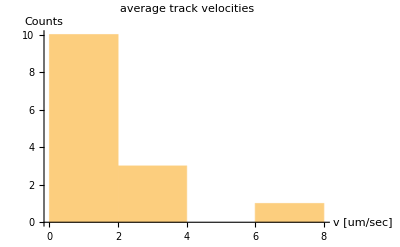
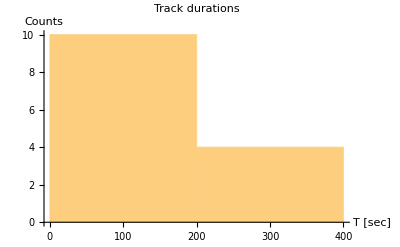
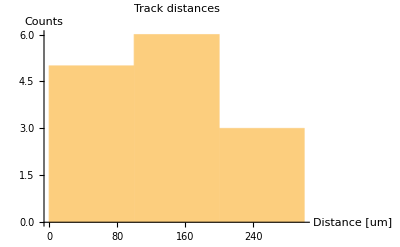
{{-Graphics-,-Graphics-,-Graphics-},{{pixelsize time= 1 sec,pixelsize space= 1 um},{Direction,Av frame2frame velocity [um/sec],track duration [sec],track total displacement [um],Start2end velocity [um/sec]},{1.,0.9229,248.,225.,0.9073},{1.,0.3389,299.,101.,0.3378},{-1.,0.3783,268.,101.,0.3769},{1.,1.1136,265.,294.,1.1094},{1.,3.2667,46.,147.,3.1957},{-1.,2.5645,63.,159.,2.5238},{0.,0.3415,42.,14.,0.3333},{1.,2.807,58.,160.,2.7586},{1.,0.3187,92.,29.,0.3152},{1.,7.973,38.,295.,7.7632},{1.,1.2778,19.,23.,1.2105},{-1.,0.3167,121.,38.,0.314},{-1.,1.871,63.,116.,1.8413},{1.,1.9,21.,38.,1.8095}}}

```mathematica
processed=pprocLocal[results[[-1]] (*tracks are the last entry in the results*),1(*pixelsize time*),1(*pixelsize space*)]
```

```mathematica
(*Example table for further analysis*)
Dataset@processed[[-1,2;;]]
```